```mathematica
(*Open file selector dialog*)fileDialogResult=SystemDialogInput["FileOpen","*.csv"];
data=Import[fileDialogResult,"CSV","SkipLines"->1];
```

```mathematica
fs=250;
```

```mathematica
(*Get timestamps in seconds*)timestepDiv=1000000000;
tims=(data[[All,1]]-data[[1,1]])/timestepDiv;

(*Extract x,y,z data*)
{x,y,z}=Transpose[data[[All,2;;4]]];
```

```mathematica
(*ListLinePlot[Transpose[{tims,z}]]*)
```

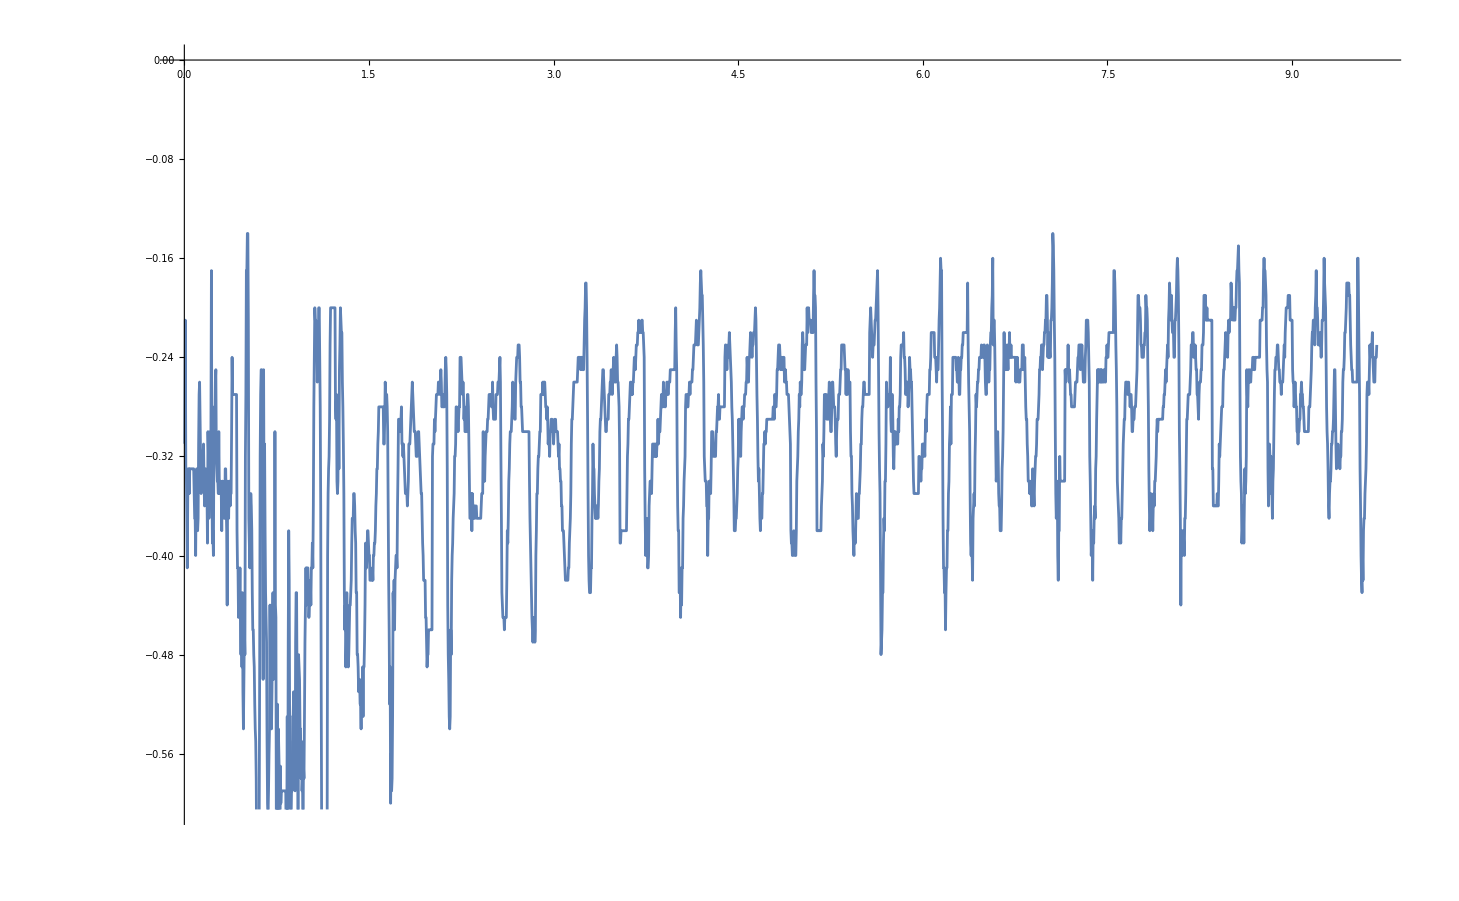

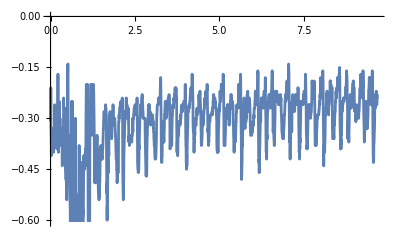

-Graphics-

```mathematica
(*Resample data*)
Xdata=TimeSeriesResample[Transpose[{tims,x}],1/fs];
ListLinePlot[Xdata]
Ydata=TimeSeriesResample[Transpose[{tims,y}],1/fs];
ListLinePlot[Xdata]
Zdata=TimeSeriesResample[Transpose[{tims,z}],1/fs];
ListLinePlot[Xdata]
```

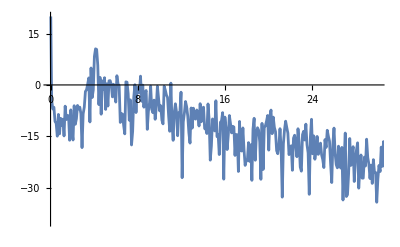

```mathematica
fftX=Abs[Fourier[Xdata[[All,2]]]];
Periodogram[Zdata[[All,2]],SampleRate->fs,PlotRange->{{0,30},{-40,20}}]
```

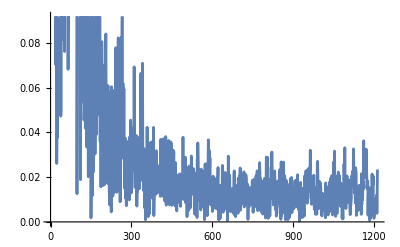

2423

2423

```mathematica
ListLinePlot[fftX[[1;;Floor[Length[fftX]/2]+1]]]
plotdata=fftX[[1;;Floor[Length[fftX]/2]+1]];
Length[Xdata]
Length[fftX]
```

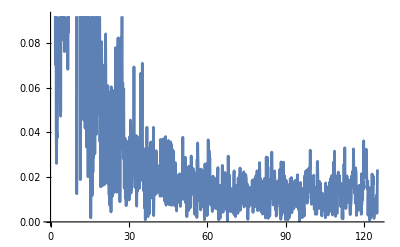

```mathematica
(*x=Range[1/fs,fs/2,fs/Floor[Length[fftX]/2]];*)
x=N@Subdivide[1/fs,fs/2,Floor[Length[fftX]/2]];
ListLinePlot[Transpose[{x,plotdata}]]
```

```mathematica
Length[x]
Length[plotdata]
```

1212

1212

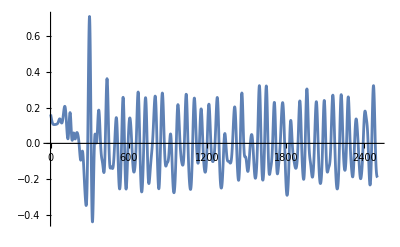

```mathematica
filtX=LowpassFilter[z,2 π 5/fs];
meanSubtractedData=#-Mean[filtX]&/@filtX;
ListLinePlot[meanSubtractedData]
```

```mathematica
(*Find indices where the signal crosses zero*)zeroCrossings=Flatten@Position[Most@Sign[meanSubtractedData]*Rest@Sign[meanSubtractedData],-1];

(*Calculate the number of samples between consecutive zero crossings*)
samplesBetweenCrossings=Differences[zeroCrossings];
```

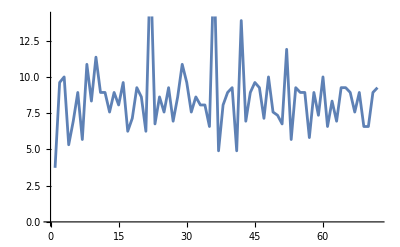

```mathematica
ListLinePlot[1/(samplesBetweenCrossings/fs)]
```

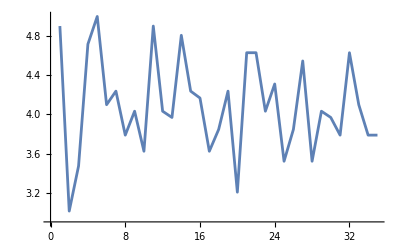

```mathematica
positiveZeroCrossings=Flatten@Position[Differences[Sign[meanSubtractedData]],2];

(*Calculate the number of samples between consecutive positive zero crossings*)
samplesBetweenPositiveZeroCrossings=Differences[positiveZeroCrossings];
ListLinePlot[1/(samplesBetweenPositiveZeroCrossings/fs)]
```